# Appendix 1

# Small Detector Approximation

```mathematica
Subscript[k, 0]=20;
Subscript[X, 0]=-5;
Subscript[X, d]=-3;
δ=0.5;
Subscript[δ, 1]=0.005;

n=100;
Ti=-0.02;
Tf=0.22;
dt=(Tf-Ti)/(n-1);

tm[0]=Ti-dt;
tm[1]=Ti;
tm[n+1]=Tf+dt;

Do[tm[i]=tm[i-1]+dt,{i,2,n}]

ψ[0,x_,t_]:=(δ^2/(2π))^(1/4)*Exp[-Subscript[k, 0]^2*δ^2]/(√(δ^2+(ⅈ*t)/2))*Exp[((2*δ^2* Subscript[k, 0] + ⅈ*(x-Subscript[X, 0]))^2)/(4*δ^2 + 2*ⅈ*t)]
K[xf_,tf_,xi_,ti_]:=1/(√(2*π*ⅈ*(tf-ti)))*Exp[(ⅈ*(xf-xi)^2)/(2*(tf-ti))]

a[1]=Abs[ψ[0,Subscript[X, d],tm[1]]]*Sqrt[Subscript[δ, 1]];
b[1]=√(1-(a[1])^2);

Do[α[0,j]=ψ[0,Subscript[X, d],tm[j]],{j,1,n+1}]

Do[Do[β[i,j]=K[Subscript[X, d],0,Subscript[X, d],tm[j]-tm[i]],{j,i+1,n+1}],{i,1,n}]

Do[Do[α[i,j]=(α[i-1,j]-α[i-1,i]*β[i,j]*Subscript[δ, 1])/b[i],{j,i+1,n+1}];a[i+1]=Abs[α[i,i+1]]*Sqrt[Subscript[δ, 1]];b[i+1]=√(1-(a[i+1])^2),{i,1,n}]
```

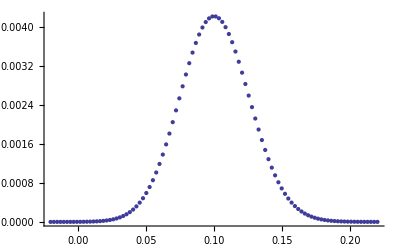

0.100794

```mathematica
Do[prob[i_]:=(∏_(k=1)^(i-1) b[k]^2)*(a[i])^2,{i,2,n,1}]
prob[1]=(a[1])^2;

ListPlot[Table[{tm[i],prob[i]},{i,n}],PlotRange->All]

tbar=(∑_(j=1)^n (tm[j]*prob[j]))/(∑_(j=1)^n prob[j])
```

```mathematica
.1-tbar
```

-0.000793868

# Random Position Approximations

```mathematica
m=10;list2={};Subscript[X, 0]=-5;Do[{{Do[acc[i]=0;bcc[i]=0,{i,1,n}];Do[{Do[tm[i]=tm[i-1]+dt,{i,2,n}],a[1]:=Abs[ψ[0,RandomReal[{Subscript[X, d]-D1/2,Subscript[X, d]+D1/2}],tm[1]]]*Sqrt[D1];
b[1]=√(1-(a[1])^2);acc[1]+=a[1];bcc[1]+=b[1];Do[α[0,j]:=ψ[0,RandomReal[{Subscript[X, d]-D1/2,Subscript[X, d]+D1/2}],tm[j]],{j,1,n+1}];Do[Do[β[i,j]:=K[RandomReal[{Subscript[X, d]-D1/2,Subscript[X, d]+D1/2}],0,RandomReal[{Subscript[X, d]-D1/2,Subscript[X, d]+D1/2}],tm[j]-tm[i]],{j,i+1,n+1}],{i,1,n}];Do[Do[α[i,j]=(α[i-1,j]-α[i-1,i]*β[i,j]*D1)/b[i],{j,i+1,n+1}];a[i+1]=Abs[α[i,i+1]]*Sqrt[D1];b[i+1]=√(1-(a[i+1])^2);acc[i+1]+=a[i+1];bcc[i+1]+=b[i+1],{i,1,n}]},{val,1,m}];Do[{acc[i]=acc[i]/m;bcc[i]=bcc[i]/m},{i,1,n}]},Do[prob2[i]=(∏_(k=1)^(i-1) bcc[k]^2)*(acc[i])^2,{i,2,n,1}];
prob2[1]=(acc[1])^2;tbar1=(∑_(j=1)^n (tm[j]*prob2[j]))/(∑_(j=1)^n prob2[j]);list2=Append[list2,{D1,tbar1}]},{D1,.00005,.05,.001}];
a3=ListLinePlot[list2,PlotRange->All,PlotStyle->{Thick,Red,Dashed},AxesOrigin->{0
,0.08},PlotLabel -> " n = 100, m = 10",AxesLabel->{Style["δ_1",Italic,10],Style["t̄",Italic,10]}]
```

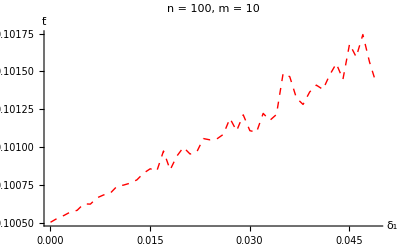

```mathematica
Non Directional & Dynamic Approach
```

```mathematica
list={};Do[list=Append[list,tm[i]],{i,1,m}];TList=Tuples[list,{n}];
```

```mathematica
Do[{Do[Tm[j]=TList[[i]][[j]],{j,1,n}]; Do[Do[If[Tm[i]≠Tm[j],{α[i,j]=(α[i-1,j]-α[i-1,i]*β[i,j]*Subscript[δ, 1])/b[i]},{α[i,j]=0}],{j,i+1,n+1}];a[i+1]=Abs[α[i,i+1]]*Sqrt[Subscript[δ, 1]];b[i+1]=√(1-(a[i+1])^2),{i,1,n}];Do[prob[i,j]=(∏_(k=1)^(j-1) b[k]^2)*(a[j])^2,{j,2,n,1}];
prob[i,1]=(a[1])^2  },{i,1,Length[TList]}];
```

```mathematica
tbar=(∑_(i=1)^Length[TList] ∑_(j=1)^n (TList[[i]][[j]]*prob[i,j]))/(∑_(i=1)^Length[TList] ∑_(j=1)^n prob[i,j])
```

0.100508

```mathematica
Directional & Dynamic Approach
```

```mathematica
Tlist={};Do[Tlist=Append[Tlist,Sort[TList[[i]]]],{i,Length[TList]}];Tlist=DeleteDuplicates[Tlist];
```

```mathematica
Do[{Do[Tm[j]=Tlist[[i]][[j]],{j,1,n}]; Do[Do[If[Tm[i]≠Tm[j],{α[i,j]=(α[i-1,j]-α[i-1,i]*β[i,j]*Subscript[δ, 1])/b[i]},{α[i,j]=0}],{j,i+1,n+1}];a[i+1]=Abs[α[i,i+1]]*Sqrt[Subscript[δ, 1]];b[i+1]=√(1-(a[i+1])^2),{i,1,n}];Do[prob[i,j]=(∏_(k=1)^(j-1) b[k]^2)*(a[j])^2,{j,2,n,1}];
prob[i,1]=(a[1])^2  },{i,1,Length[Tlist]}]
```

```mathematica
tbar=(∑_(i=1)^Length[Tlist] ∑_(j=1)^n (Tlist[[i]][[j]]*prob[i,j]))/(∑_(i=1)^Length[Tlist] ∑_(j=1)^n prob[i,j])
```